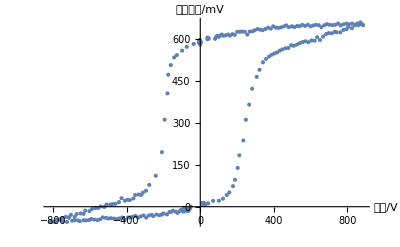
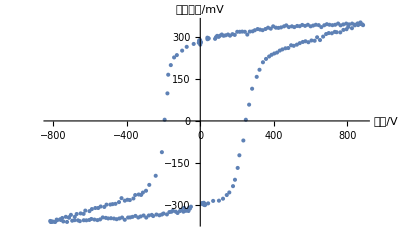

```mathematica
VO=Import["E:\\002课程\\0近代物理实验\\铁电测量\\data\\950.txt","Table"];
meany1=Mean[VO[[1;;Length[VO],2]]];
V=VO;
V[[All,2]]=V[[All,2]]-meany1;
{ListPlot[VO,AxesLabel->{"电压/V","极化强度/mV"}],ListPlot[V,AxesLabel->{"电压/V","极化强度/mV"}]}
```

Check 并绘图

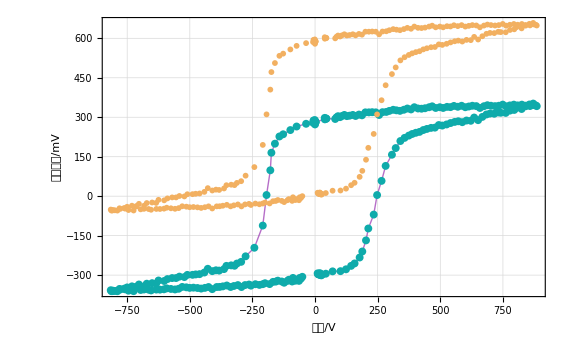

{-815.6,885.1}

```mathematica
Show[
ListLinePlot[V,PlotStyle->{RGBColor[0.55,0.1,0.66,0.63],Thin}],

ListPlot[V,PlotStyle->{RGBColor[0.06,0.67,0.67],PointSize[0.01]},PlotLegends->Placed[{"平移后数据"},{Left,Top}]],

ListPlot[VO,PlotStyle->{RGBColor[0.95,0.69,0.38]},PlotLegends->Placed["",{Left,Top}]],

AxesLabel->{"电压/V","极化强度/mV"},PlotStyle->Large,
PlotRange->All,GridLines->Automatic,Frame->True]

sorteVMax=Sort[V,#[[1]]>#2[[1]]&];
VMaxElements=Take[sorteVMax,1];
sorteVMin=Sort[V,#[[1]]<#2[[1]]&];
VMinElements=Take[sorteVMin,1];
{VMinElements[[1,1]],VMaxElements[[1,1]]}
(*真实电压扫描范围*)
```

确定最右上角的元素，并取之后40点线性拟合

```mathematica
sorteBigX=Sort[V,#[[1]]>#2[[1]]&];
BiggestX=Take[sorteBigX,2]
BiggestXpositions=Position[V,#]&/@BiggestX//Flatten
nB=BiggestXpositions[[1]];
linesP=Fit[V[[nB;;nB+40]],{1,x},x];
{a,b}=CoefficientList[linesP,x];
PsP=a;
Print["PsP=",a]
```

{{885.1,342.222},{881.3,344.892}}

{65,66}

PsP=320.29

确定最左下角的元素，并取之后40点线性拟合

```mathematica
sorteSmallX=Sort[V,#[[1]]<#2[[1]]&];
SmallestX=Take[sorteSmallX,2]
SmallestXpositions=Position[V,#]&/@SmallestX//Flatten
nS=SmallestXpositions[[1]];
linesN=Fit[V[[nS;;nS+40]],{1,x},x];
{a,b}=CoefficientList[linesN,x];
PsN=a;
Print["PsN=",a]
```

{{-815.6,-357.418},{-813.2,-360.928}}

{191,192}

PsN=-330.216

确定磁滞回线和X轴的两个交点

```mathematica
sorteNearY=Sort[V,Abs[#[[2]]]<Abs[#2[[2]]]&];
(*然后取排序后Y数值最接近0的两个元素*)
nearestYElements=Take[sorteNearY,6]
(*获取这些元素在原数据中的位置*)
YP=Position[V,#]&/@nearestYElements//Flatten
```

{{247.7,4.29091},{-193.7,4.39731},{265.5,58.1674},{234.2,-69.9303},{-178.6,98.4515},{-208.7,-111.649}}

{25,153,26,24,152,154}

```mathematica
x1=25;
x2=153;
```

-881.137+3.53565 x

EcP=249.215

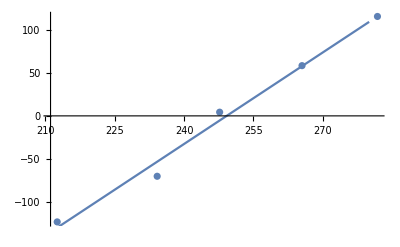

```mathematica
fEcP=Fit[V[[x1-2;;x1+2]],{1,x},x]

solcP=Solve[fEcP==0,x];
EcP=x/.solcP[[1]];
Print["EcP=",EcP]
Show[ListPlot[V[[x1-2;;x1+2]]],
Plot[fEcP,{x,180,280}]
]
```

```mathematica
(*fEcP=Interpolation[V[[x1-2;;x1+2]]];
solcP=Reduce[fEcP[x]==0,x];
EcP=x/.solcP[[1]]
Show[ListPlot[V[[x1-2;;x1+2]]],
Plot[fEcP[x],{x,180,280}],
PlotRange->All
]*)
```

1293.33+6.67482 x

EcN=-193.763

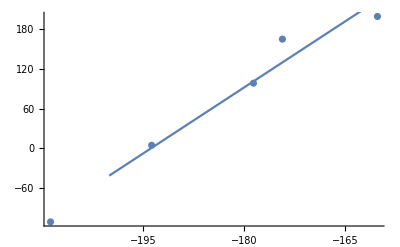

```mathematica
fEcN=Fit[V[[x2-3;;x2+1]],{1,x},x]
solcN=Solve[fEcN==0,x];
EcN=x/.solcN[[1]];
Print["EcN=",EcN]
Show[ListPlot[V[[x2-3;;x2+1]]],
Plot[fEcN,{x,-200,-160}]
]
```

```mathematica
(*fEcN=Interpolation[V[[165-4;;165+4]]];
Plot[fEcN[x],{x,-240,-200}]
solcN=Solve[fEcN[x]==0,x];
EcN=x/.solcN[[1]]*)
```

确定磁滞回线和Y轴的两个交点

```mathematica
sorteNearX=Sort[V,Abs[#[[1]]]<Abs[#2[[1]]]&];
(*然后取排序后X轴数值最接近0的N个元素*)
nearestXElements=Take[sorteNearX,20]
(*获取这些元素在原数据中的位置*)
XP=Position[V,#]&/@nearestXElements//Flatten
```

{{-0.1,279.633},{-0.2,272.643},{-0.9,289.243},{1.3,279.552},{1.4,281.192},{1.8,280.399},{-2,284.617},{-2.1,284.719},{2.2,282.865},{-2.4,284.839},{-2.4,285.247},{-3.9,281.553},{-4,285.025},{-6.2,287.495},{-8,279.255},{10.3,-293.383},{11.7,-296.454},{15.9,-296.56},{16.2,-297.968},{16.7,-296.398}}

{135,134,132,137,140,142,141,143,139,138,136,130,133,131,144,11,12,10,9,8}

```mathematica
y1=135;
```

```mathematica
fPrP=Fit[V[[y1-10;;y1+10]],{1,x},x];
{a,b}=CoefficientList[fPrP,x];
PrP=a;
Print["PrP=",a]
fPrN=Fit[Flatten[{V[[240;;250]],V[[1;;10]]},1],{1,x},x];
{a,b}=CoefficientList[fPrN,x];
PrN=a;
Print["PrN=",a]
```

PrP=283.259

PrN=-301.239

```mathematica
parameter={EcP,EcN,PrP,PrN,PsP,PsN}
Print[NumberForm[EcP,5]," & ",NumberForm[EcN,5]," & ",NumberForm[PrP,5]," & ",NumberForm[PrN,5]," & ",NumberForm[PsP,5]," & ",NumberForm[PsN,5]]
```

{249.215,-193.763,283.259,-301.239,320.29,-330.216}

249.22 & -193.76 & 283.26 & -301.24 & 320.29 & -330.22

```mathematica
Show[
ListPlot[VO,PlotStyle->{RGBColor[0.15,0.72,0.3]},PlotLegends->{"原始数据"}],
ListLinePlot[V,PlotLegends->{"消除偏移数据"}],


ListPlot[{Callout[{0,PrP},"PrP="<>ToString[PrP],{40,PrP-100}],Callout[{0,PrN},"PrN="<>ToString[PrN],{40,PsN+100}],
Callout[{EcP,0},"EcP="<>ToString[EcP],{EcP+40,50}],Callout[{EcN,0},"EcN="<>ToString[EcN],{EcN-40,50}]},
PlotStyle->{Blue,PointSize->Medium}
],


ListPlot[{Callout[{0,PsP},"PsP="<>ToString[PsP],{40,PsP+100}],Callout[{0,PsN},"PsN="<>ToString[PsN],{40,PsN-100}]},
PlotStyle->{Red,PointSize->Medium}
],


Plot[linesP,{x,-50,800},PlotStyle->{Red,Dashed},PlotLegends->{"线性拟合"}],
Plot[linesN,{x,-800,50},PlotStyle->{Red,Dashed}],
AxesLabel->{"电压/V","极化强度/mV"},
PlotStyle->Large,

PlotRange->All
]
```

-Graphics-

```mathematica
Show[
ListPlot[VO,PlotStyle->{RGBColor[0.15,0.72,0.3]},PlotLegends->Placed[{"原始数据"},{Left,Top}]],
ListLinePlot[V,PlotLegends->Placed[{"消除偏移数据"},{Left,Top}]],
Plot[linesN,{x,-850,50},PlotStyle->{Red,Dashed}],
Plot[linesP,{x,-50,820},PlotStyle->{Red,Dashed},PlotLegends->Placed[{"线性拟合"},{Left,Top}]],


ListPlot[{Callout[{0,PrP},"P_rP="<>ToString[PrP],{40,PrP-100}],Callout[{0,PrN},"P_rN="<>ToString[PrN],{40,PsN+100}],
Callout[{EcP,0},"E_cP="<>ToString[EcP],{EcP+40,50}],Callout[{EcN,0},"E_cN="<>ToString[EcN],{EcN-40,50}]},
PlotStyle->{Blue,PointSize->Medium}
],
ListPlot[{Callout[{0,PsP},"P_sP="<>ToString[PsP],{40,PsP+100}],Callout[{0,PsN},"P_sN="<>ToString[PsN],{40,PsN-100}]},
PlotStyle->{Red,PointSize->Medium}
],




AxesLabel->{"电压/V","极化强度/mV"},
PlotStyle->Large,

PlotRange->All,
GridLines->Automatic,
Frame->True
]
```

-Graphics-